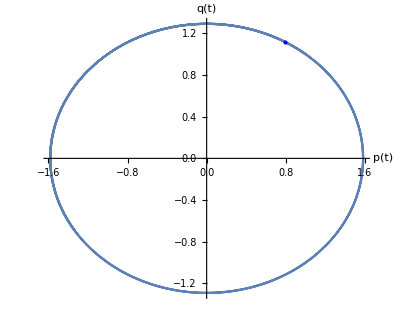

```mathematica
H=p[t]^2/(2*1/2)+1/2 3 q[t]^2;
soln=DSolve[{D[H,p[t]]==q'[t],p'[t]==-D[H,q[t]]},{q[t],p[t]},t];
point=Point[{p[t],q[t]}/.(soln/.{C[1]->1,C[2]->1})/.{t->-2.5}];
params={C[1]->1,C[2]->1};
spsoln=soln/.params;
fig1=ParametricPlot[{p[t],q[t]}/.spsoln,{t,0,2Pi},AxesLabel->{"p(t)","q(t)"},
Epilog->{Blue,PointSize@Large,point},
AspectRatio->Automatic]
```

```mathematica
Export["~/school/FA22/PHYS163a/figs/phase1.png",fig1]
```

~/school/FA22/PHYS163a/figs/phase1.png

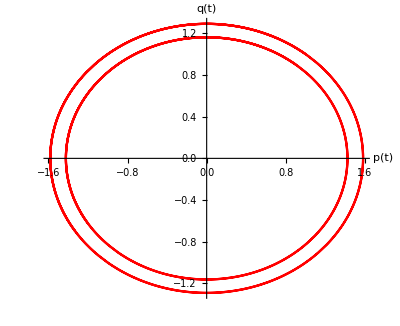

```mathematica
(* Shade the annular region *)

fig2=Show[
ParametricPlot[{p[t],q[t]}/.spsoln,{t,0,2Pi},AxesLabel->{"p(t)","q(t)"},
AspectRatio->Automatic,PlotStyle->Red],
ParametricPlot[{0.9*p[t],0.9*q[t]}/.spsoln,{t,0,2Pi},PlotStyle->Red]]
```

```mathematica
Export["~/school/FA22/PHYS163a/figs/phase2.png",fig2]
```

~/school/FA22/PHYS163a/figs/phase2.png

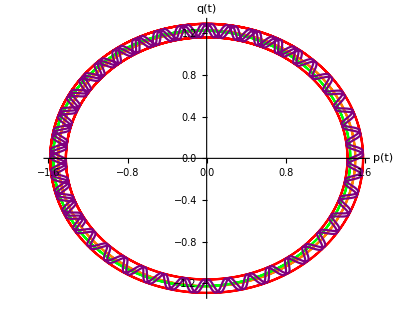

```mathematica
e={0.9*p[t],0.9*q[t]};
ede={p[t],q[t]};
ex1={0.95*p[t],0.95*q[t]};
ex2={0.95p[t]-0.05,0.95q[t]};
ex3={(0.95+Sin[100t]/20)p[t],(0.95+Sin[100t]/20)q[t]};
plts =(#/.spsoln&)/@ {e,ede,ex1,ex2,ex3};
fig3=ParametricPlot[plts,{t,0,2Pi},
AxesLabel->{"p(t)","q(t)"},
PlotStyle->Directive/@{Red,Red,Orange,Green,Purple}]
```

```mathematica
Export["~/school/FA22/PHYS163a/figs/phase3.png",fig3]
```

~/school/FA22/PHYS163a/figs/phase3.png

Question 2

```mathematica
DSolve[{D[ρ[q,p,t],t]==-p/m D[ρ[q,p,t],q],ρ[q,p,0]==DiracDelta[q] Exp[-p^2/(2m k T)]/(√(2π m k T))},ρ[q,p,t],{q,p,t}]
```

DSolve[{ρ^(0,0,1)[q,p,t]==-(p ρ^(1,0,0)[q,p,t])/m,ρ[q,p,0]==(ⅇ^(-p^2/(2 k m T)) DiracDelta[q])/(√(2 π) √(k m T))},ρ[q,p,t],{q,p,t}]

```mathematica
H2=p^2/(2m);
D[ρ[q,p,t],t]==-D[H2,p]D[ρ[q,p,t],q]+D[H2,q]D[ρ[q,p,t],p]
```

ρ^(0,0,1)[q,p,t]==-(p ρ^(1,0,0)[q,p,t])/m

```mathematica
DSolve[Derivative[0,0,1][ρ][q,p,t]==-(p Derivative[1,0,0][ρ][q,p,t])/m,{ρ[q,p,t],ρ[q,p,t]},{t}]
```

{{ρ[q,p,t]→C[1]+-(p ρ^(1,0,0)[q,p,K[1]])/mK[1]1t}}

```mathematica
Integrate[DiracDelta[x-y],{x,-Infinity,Infinity}]
```

ConditionalExpression[1, y∈ℝ]

```mathematica
Integrate[p^2 Exp[-p^2/(2m k T)],{p,-Infinity,Infinity}]
```

ConditionalExpression[(√(2 π))/(1/(k m T))^(3/2), Re[1/(k m T)]>0]

```mathematica
Simplify[ConditionalExpression[(√(2 π))/(1/(k m T))^(3/2), Re[1/(k m T)]>0],Assumptions->{k,m,t}>0.1]
```

ConditionalExpression[(√(2 π))/(1/(k m T))^(3/2), Re[1/(k m T)]>0]

```mathematica
Solve[x^(1/2)==1/(1/x)^(1/2)]
```

{{}}

```mathematica
1/(1/(√x))
```

√x

```mathematica
(√(2 π))/(1/(k m T)^(3/2))
```

```mathematica
(√(2 π) (k m T)^(3/2))/(√(2π m k T))
```

k m T

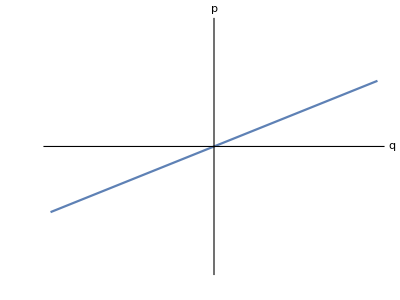

```mathematica
fig4=ParametricPlot[{q,q 2/5},{q,-1,1},PlotRange->{{-1,1},{-0.75,0.75}},AxesLabel->{"q","p"},Ticks->None]
```

```mathematica
Export["~/school/FA22/PHYS163a/figs/phase4.png",fig4]
```

~/school/FA22/PHYS163a/figs/phase4.png